# Cosmomathica

Adrian Vollmer, Institute for theoretical Physics, Universität Heidelberg, 2014

This notebook demonstrates how to use the Cosmomathica package version 0.3.

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

A short description for all functions

```mathematica
?Transfer
```

Transfer[OmegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (high baryon case). It takes the total matter density Ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant h as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function for CDM, baryons, both, or with no baryons or no wiggles.

```mathematica
?TFPower
```

"TFPower[OmegaM, OmegaB, OmegaMN, DegenNu, OmegaL, h, z] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (mixed matter case). It takes the total matter density Ω_M, the baryon density Ω_b, the massive neutrino density Ω_ν, the integer number of degenerate massive neutrino species, the dark energy density Ω_L, the dimensionless Hubble constant h, and the redshift z as input, and return the transfer function at the given redshift."

```mathematica
?Halofit
```

"Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: linearly with the BBKS alogorithm, nonlinear with the algorithm by Peacock and Dobbs, or nonlinearly with the Halofit algorithm) at 20 different values of the scale factor and the convergence power spectrum in tabulated form."

```mathematica
?CosmicEmu
```

"CosmicEmu[omegaM, omegaB, sigma8, ns, w] provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon."

```mathematica
?FrankenEmu
```

"FrankenEmu[omegaM, omegaB, h, sigma8, ns, w] provides an interface to FrankenEmu by Earl Lawrence. It takes ω_M, ω_b, h, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon. The Hubble parameter h can also be omitted, in which case it will be determined from the CMB just as in CosmicEmu. Additional cosmological parameters are only returned if h is missing."

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
?Copter
```

"Copter[OmegaM, OmegaB, h, ns, sigma8, transfer, z, type] provides an interface to Copter by Jordan Carlson. It takes Ω_M, Ω_b, h, n_s, σ_8, the transfer function in shape of a list of value pairs and returns the power spectrum and other quantities. The 'type' variable specifies which pertubration theory is used and must take one of the following values (as a string): 'SPT' (Standard PT), 'RPT' (Renormalized PT), 'LPT' (Lagrangian PT), 'FWT' (Flowing with time, TRG), 'LargeN', 'HSPT' (Higher order PT), 'NW' (no wiggles, Eisenstein&Hu algorithm), 'Linear'. Several options can be specified."

```mathematica
?Class
```

Class["parameter1" -> "value1",...] runs Class. You need to specifiy all Class parameters in the form of options. Cosmomathica then writes all options into an ini-file, where each line contains "parameter = value". This file is fed to Class and the output is returned.

### Transfer

This is how you call Eisenstein&Hu’s Transfer function code

```mathematica
tfdata=Transfer[.12,.3,2.7,.67];
```

To see what kind of data has been returned, type this

```mathematica
tfdata[[All,1]]
```

{Transfer[soundhorizon],Transfer[peak],Transfer[kvalues],Transfer[full],Transfer[baryon],Transfer[cdm],Transfer[nowiggles],Transfer[zerobaryons]}

To access it, use the replacement rules, e.g. for the sound horizon

```mathematica
Transfer["soundhorizon"]/.tfdata
```

128.773

or for the various transfer functions

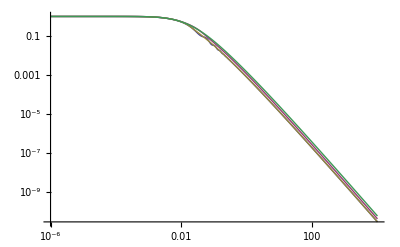

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Transfer["kvalues"]/.tfdata,pk}],{pk,{
Transfer["full"],
Transfer["cdm"],
Transfer["nowiggles"],
Transfer["zerobaryons"]
}/.tfdata}],Joined->True]
```

The mixed matter case is a bit simpler :

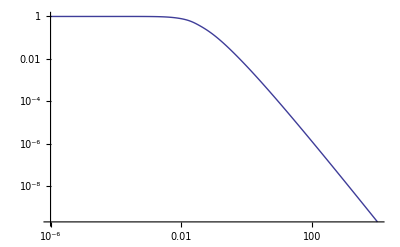

```mathematica
ListLogLogPlot[TFPower[.3,.05,0,0,.7,.7,0.],Joined->True]
```

### Halofit

Call the Halofit+ code

```mathematica
hfdata=Halofit[.25,.75,.259,.8,.9,1.,1.5];
```

View the output data options

```mathematica
hfdata[[All,1]]
```

{Halofit[avalues],Halofit[kvalues],Halofit[ellvalues],Halofit[kappaBBKS],Halofit[BBKS],Halofit[kappaPD96],Halofit[PD96],Halofit[kappaHalofit],Halofit[Halofit]}

Plot the matter power spectrum using the Halofit algorithm at different redshifts

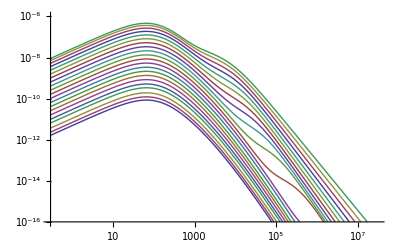

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["kvalues"]/.hfdata,pk}],
{pk,Halofit["Halofit"]/.hfdata}],
Joined->True,PlotRange->{1*^-16,1*^-6}]
```

Note that Halofit[“Halofit”] returns a list of lists, each of which corresponds to the power spectrum at a different redshift or scale factor. The scale factors are as follows

```mathematica
Halofit["avalues"]/.hfdata
```

{0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.}

Plot the convergence power spectrum using three different algorithms

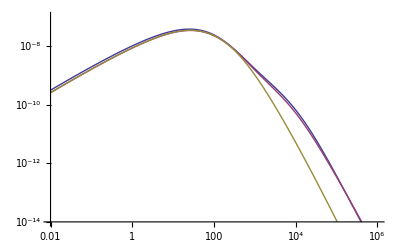

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["ellvalues"]/.hfdata,kappa}],{kappa,{
Halofit["kappaHalofit"],
Halofit["kappaPD96"],
Halofit["kappaBBKS"]
}/.hfdata}],Joined->True,PlotRange->{1*^-14,1*^-7}]
```

### Cosmic Emulator

Call the Cosmic Emulator

```mathematica
cedata=CosmicEmu[.15,.022,.8,.9,-1];
```

View the output

```mathematica
cedata[[All,1]]
```

{CosmicEmu[zvalues],CosmicEmu[pk],CosmicEmu[soundhorizon],CosmicEmu[zlss],CosmicEmu[dlss],CosmicEmu[hubblecmb]}

Redshift of last scattering

```mathematica
CosmicEmu["zlastscatter"]/.cedata
```

CosmicEmu[zlastscatter]

Power spectrum at the following redshifts

```mathematica
CosmicEmu["zvalues"]/.cedata
```

{1.,0.666667,0.428571,0.25,0.111111,0.}

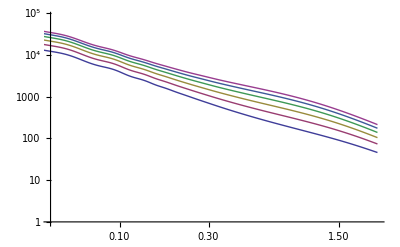

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,CosmicEmu["pk"]/.cedata}],Joined->True]
```

### FrankenEmu

Call FrankenEmu

```mathematica
fedata=FrankenEmu[.15,.022,.7,.85,.9,-1];
```

View the output

```mathematica
fedata[[All,1]]
```

{FrankenEmu[zvalues],FrankenEmu[pk]}

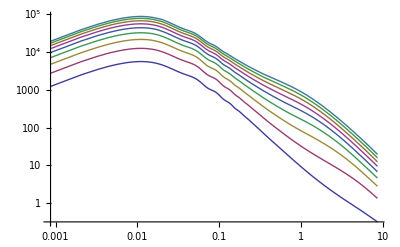

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,FrankenEmu["pk"]/.fedata}],Joined->True]
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{Tcmb→2.7255,OmegaNu→0,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→none,WantCMB→True,WantTransfer→True,WantCls→True,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,TransferHighPrecision→False,WantScalars→True,WantVectors→True,WantTensors→True,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→3000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→0.9,TransferKperLogInt→0,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→True,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
cambdata=CAMB[.2,.05,.75,.67,-1.,WantTransfer->True,DoLensing->False,TransferRedshifts->{1.5,0.}];
```

```mathematica
cambdata[[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[CLvector],CAMB[CLtensor],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
cambdata[[1]]
```

CAMB[age]→14.7873

Age of the universe:

```mathematica
CAMB["age"]/.cambdata
```

14.7873

There is a σ_8 for each redshift and for each spectral index

```mathematica
CAMB["sigma8"]/.cambdata
```

{{0.35308},{0.680405}}

Plot the scalar angular power spectrum

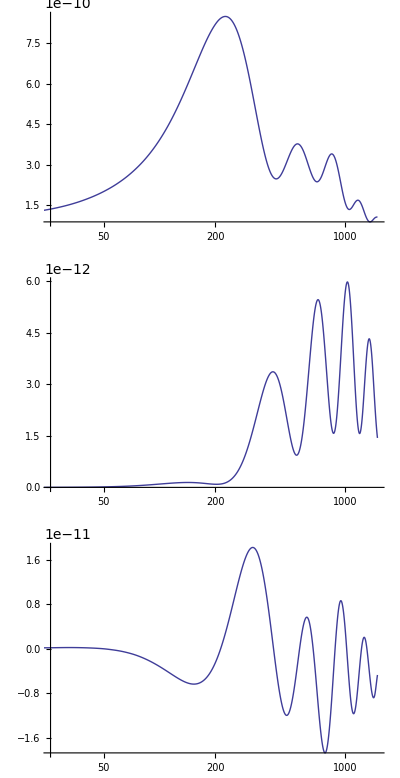

```mathematica
GraphicsGrid@Transpose@List@Table[ListLogLinearPlot[plot,Joined->True,PlotRange->All],{plot,CAMB["CLscalar"]/.cambdata}]
```

In version Nov13, CAMB computes the power spectrum at more than just the requested redshifts :

```mathematica
CAMB["redshifts"]/.cambdata
```

{9.,8.,7.,6.,5.,4.,3.,2.,1.5,1.,0.}

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

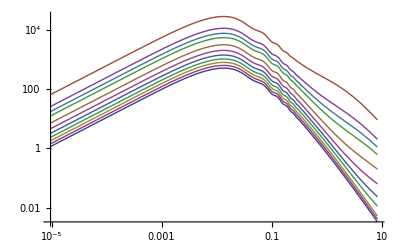

```mathematica
ListLogLogPlot[CAMB["PSnonlinear"]/.cambdata,Joined->True]
```

Plot the CDM transfer function at the first redshift

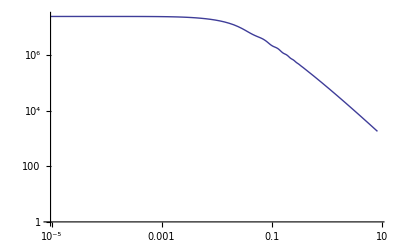

```mathematica
ListLogLogPlot[(CAMB["Transfer"]/.cambdata)[[-1,All,{1,2}]],Joined->True]
```

### Copter

There are some options to the Copter function that influence precision and speed (see Copter source code for details):

```mathematica
Options[Copter]
```

{zInitial→100,Neta→50,kcut→10,epsrel→1/10000,qmin→1/10000,qmax→100,order→3,formula→1}

Call Copter (needs the transfer function from above)

```mathematica
copdata=Copter[.25,.05,.7,.9,.8,Transpose[{Transfer["kvalues"],Transfer["full"]}/.tfdata],0,"SPT"];
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Part::partw: Part 2 of Transpose[Partition[Null, 4]] does not exist.

Part::partw: Part 3 of Transpose[Partition[Null, 4]] does not exist.

Part::partw: Part 4 of Transpose[Partition[Null, 4]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

View the output

```mathematica
copdata[[All,1]]
```

{Copter[kvalues],Copter[P11],Copter[P12],Copter[P22],Copter[1L-Propagator]}

```mathematica
ListLogLogPlot[{Transpose[{Copter["kvalues"],Copter["P11"]}/.copdata],
Transpose[{Copter["kvalues"],Copter["P12"]}/.copdata],
Transpose[{Copter["kvalues"],Copter["P22"]}/.copdata]},Joined->True]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{1.×10^-6, 1.02329×10^-6, 1.04713×10^-6, 1.07152×10^-6, 1.09648×10^-6, 1.12202×10^-6, 1.14815×10^-6, 1.1749×10^-6, 1.20226×10^-6, 1.23027×10^-6, 1.25893×10^-6, 1.28825×10^-6, 1.31826×10^-6, 1.34896×10^-6, 1.38038×10^-6, 1.41254×10^-6, « 19 », 2.23872×10^-6, 2.29087×10^-6, 2.34423×10^-6, 2.39883×10^-6, 2.45471×10^-6, 2.51189×10^-6, 2.5704×10^-6, 2.63027×10^-6, 2.69153×10^-6, 2.75423×10^-6, 2.81838×10^-6, 2.88403×10^-6, 2.95121×10^-6, 3.01995×10^-6, 3.0903×10^-6, « 951 »}, « 1 »} cannot be transposed.

Part::partw: Part 2 of Transpose[Partition[Null, 4]] does not exist.

Part::partw: Part 3 of Transpose[Partition[Null, 4]] does not exist.

Part::partw: Part 4 of Transpose[Partition[Null, 4]] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {{1.×10^-6, 1.02329×10^-6, 1.04713×10^-6, 1.07152×10^-6, 1.09648×10^-6, 1.12202×10^-6, 1.14815×10^-6, 1.1749×10^-6, 1.20226×10^-6, 1.23027×10^-6, 1.25893×10^-6, 1.28825×10^-6, 1.31826×10^-6, 1.34896×10^-6, 1.38038×10^-6, 1.41254×10^-6, « 19 », 2.23872×10^-6, 2.29087×10^-6, 2.34423×10^-6, 2.39883×10^-6, 2.45471×10^-6, 2.51189×10^-6, 2.5704×10^-6, 2.63027×10^-6, 2.69153×10^-6, 2.75423×10^-6, 2.81838×10^-6, 2.88403×10^-6, 2.95121×10^-6, 3.01995×10^-6, 3.0903×10^-6, « 951 »}, « 1 »} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Null, 4.].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

-Graphics-

The growth function can be computed with a separate function

```mathematica
zrange=Range[0,50,.1];
copgrowth=CopterGrowth[.25,.05,.7,.9,zrange];
ListLogPlot[Transpose[{zrange,copgrowth}],Joined->True]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1., 1.1, 1.2, 1.3, 1.4, 1.5, 1.6, 1.7, 1.8, 1.9, 2., 2.1, 2.2, 2.3, 2.4, 2.5, 2.6, 2.7, 2.8, 2.9, 3., 3.1, 3.2, 3.3, 3.4, 3.5, 3.6, 3.7, 3.8, 3.9, 4., 4.1, 4.2, 4.3, 4.4, 4.5, 4.6, 4.7, 4.8, 4.9, « 451 »}, Null} cannot be transposed.

ListLogPlot::lpn: Transpose[{{0., 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1., 1.1, 1.2, 1.3, 1.4, 1.5, 1.6, 1.7, 1.8, 1.9, 2., 2.1, 2.2, 2.3, 2.4, 2.5, 2.6, 2.7, 2.8, 2.9, 3., 3.1, 3.2, 3.3, 3.4, 3.5, 3.6, 3.7, 3.8, 3.9, 4., 4.1, 4.2, 4.3, 4.4, 4.5, 4.6, 4.7, 4.8, 4.9, « 451 »}, Null}] is not a list of numbers or pairs of numbers.

ListLogPlot[Transpose[{{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.,20.1,20.2,20.3,20.4,20.5,20.6,20.7,20.8,20.9,21.,21.1,21.2,21.3,21.4,21.5,21.6,21.7,21.8,21.9,22.,22.1,22.2,22.3,22.4,22.5,22.6,22.7,22.8,22.9,23.,23.1,23.2,23.3,23.4,23.5,23.6,23.7,23.8,23.9,24.,24.1,24.2,24.3,24.4,24.5,24.6,24.7,24.8,24.9,25.,25.1,25.2,25.3,25.4,25.5,25.6,25.7,25.8,25.9,26.,26.1,26.2,26.3,26.4,26.5,26.6,26.7,26.8,26.9,27.,27.1,27.2,27.3,27.4,27.5,27.6,27.7,27.8,27.9,28.,28.1,28.2,28.3,28.4,28.5,28.6,28.7,28.8,28.9,29.,29.1,29.2,29.3,29.4,29.5,29.6,29.7,29.8,29.9,30.,30.1,30.2,30.3,30.4,30.5,30.6,30.7,30.8,30.9,31.,31.1,31.2,31.3,31.4,31.5,31.6,31.7,31.8,31.9,32.,32.1,32.2,32.3,32.4,32.5,32.6,32.7,32.8,32.9,33.,33.1,33.2,33.3,33.4,33.5,33.6,33.7,33.8,33.9,34.,34.1,34.2,34.3,34.4,34.5,34.6,34.7,34.8,34.9,35.,35.1,35.2,35.3,35.4,35.5,35.6,35.7,35.8,35.9,36.,36.1,36.2,36.3,36.4,36.5,36.6,36.7,36.8,36.9,37.,37.1,37.2,37.3,37.4,37.5,37.6,37.7,37.8,37.9,38.,38.1,38.2,38.3,38.4,38.5,38.6,38.7,38.8,38.9,39.,39.1,39.2,39.3,39.4,39.5,39.6,39.7,39.8,39.9,40.,40.1,40.2,40.3,40.4,40.5,40.6,40.7,40.8,40.9,41.,41.1,41.2,41.3,41.4,41.5,41.6,41.7,41.8,41.9,42.,42.1,42.2,42.3,42.4,42.5,42.6,42.7,42.8,42.9,43.,43.1,43.2,43.3,43.4,43.5,43.6,43.7,43.8,43.9,44.,44.1,44.2,44.3,44.4,44.5,44.6,44.7,44.8,44.9,45.,45.1,45.2,45.3,45.4,45.5,45.6,45.7,45.8,45.9,46.,46.1,46.2,46.3,46.4,46.5,46.6,46.7,46.8,46.9,47.,47.1,47.2,47.3,47.4,47.5,47.6,47.7,47.8,47.9,48.,48.1,48.2,48.3,48.4,48.5,48.6,48.7,48.8,48.9,49.,49.1,49.2,49.3,49.4,49.5,49.6,49.7,49.8,49.9,50.},Null}],Joined→True]

## Class

Every parameter is configured by options. We build a .ini file from them and pass it on to Class. So every option of the form “key”->”value” becomes one line in the .ini file of the form “key = value”. Note that all values need to be strings. For details, read the file explanatory.ini which comes with the Class package.

```mathematica
classdata=Class["h" -> ".6","Omega_k"->"0.2","n_s"->".9", "Omega_b"->"0.02",
"output"->"mTk,mPk",
"z_pk"->"0,1,2",
"gauge"->"synch",
"non linear"->"",
"P_k_max_h/Mpc"->"10",
"modes"->"s",
"format"->"camb"];
```

View the output

```mathematica
classdata[[All,1]]
```

{Class[kvalues],Class[tauvalues],Class[sigma8],Class[transfer],Class[PSlinear],Class[background]}

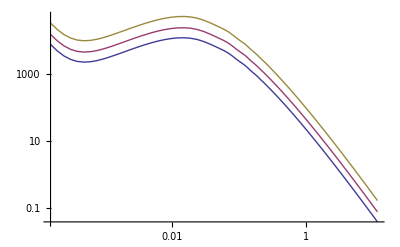

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose@{Class["kvalues"]/.classdata,(Class["PSlinear"]/.classdata)[[i]]},{i,{1,5,10}}],Joined->True]
```